This solves the so-called Polar Wave Equation.
u_xx - (1/r u_r + 1/r^2 u_tt) = 0 .  
Second derivative in the r direction *minus* the second derivative in the theta direction = 0.

f10 means value is 1 and slope is 0 at r = R.

```mathematica
f10[r_, k_Integer, R_]:= Module[{β = Sqrt[k^2-1], logR = Log[R], cosR, sinR},
Which[k<0, 0, (*Return 0 but this is an error *)
k == 0, 1,
r == 0, 0,  (* return 0 if r = 0 *)
k == 1, r/R(1-Log[r/R]),
k > 1,logR = Log[R];
cosR = Cos[β logR];
sinR = Sin[β logR];
r/(β R) ( (β cosR +sinR )Cos[β Log[r]] +( β sinR-cosR )Sin[β Log[r]])
]
]
```

f01 means value is 0 and slope is 1 at r = R.

```mathematica
f01[r_, k_Integer, R_]:= Module[{β = Sqrt[k^2-1], logR = Log[R], cosR, sinR},
Which[k<0, 0, (*Return 0 but this is an error *)
k == 0, (r^2/R - R)/2,
r == 0, 0,  (* return 0 if r = 0 *)
k == 1, r Log[r/R],
k > 1,
cosR = Cos[β logR];
sinR = Sin[β logR];
r/β ( -sinR Cos[β Log[r]] +cosR Sin[β Log[r]])
]
]
```

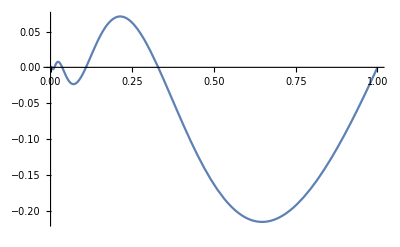

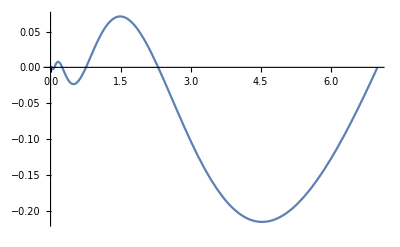

```mathematica
Plot[f01[r, 3, 1],{r, 0, 1}]
Plot[f01[r, 3, 7]/7,{r, 0, 7}]
```

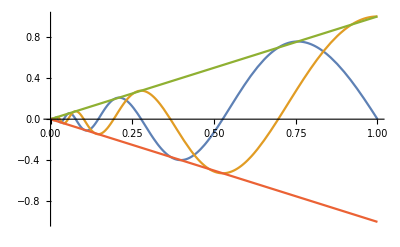

```mathematica
k = 5;
Plot[{-k f01[r, k, 1],f10[r,k,1], r, -r},{r, 0, 1}]
```

```mathematica
f = c1 r Cos[b Log[r]] + c2 r Sin[b Log[r]]
```

c1 r Cos[b Log[r]]+c2 r Sin[b Log[r]]

```mathematica
fp = Simplify@D[f, r]
```

(c1+b c2) Cos[b Log[r]]+(-b c1+c2) Sin[b Log[r]]

```mathematica
Simplify@Solve[{f == 1, fp == 0}, {c1, c2}]
```

{{c1→(b Cos[b Log[r]]+Sin[b Log[r]])/(b r),c2→((b-Cot[b Log[r]]) Sin[b Log[r]])/(b r)}}

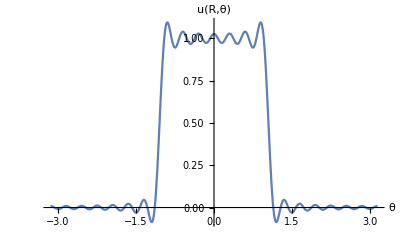

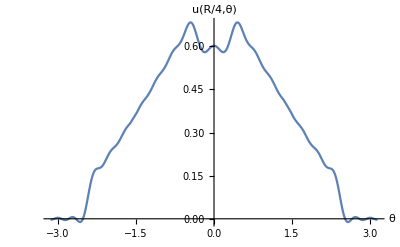

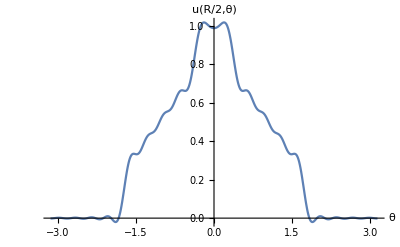

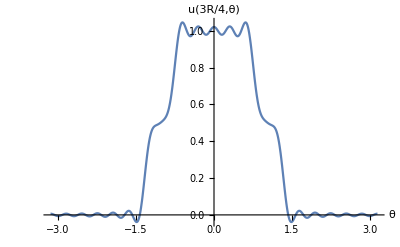

```mathematica
R = 3;
nMax = 20;
alpha = Pi/3;  (* u = 1 for -alpha < theta < alpha *)
cn= Table[2 Sin[n alpha]/(n Pi), {n, 1, nMax}];
c0 = alpha/Pi;
pR =Plot[c0+∑_(n=1)^nMax cn[[n]] Cos[n t], {t, -Pi, Pi}, AxesLabel ->{θ, "u(R,θ)"}] (* u(R, theta *)
fofrt[r_, t_] :=c0 +∑_(n=1)^nMax cn[[n]]*f10[r, n, R]Cos[n t];
fofrt[r_, t_] := c0 + Sum[cn[[n]]*f10[r, n, R]Cos[n t], {n, 1, nMax}]
pR4 = Plot[fofrt[R/4, t], {t, -Pi, Pi}, PlotRange -> All, AxesLabel ->{θ, "u(R/4,θ)"}] (* Plot at r = R/4 *)
pR2 = Plot[fofrt[R/2, t], {t, -Pi, Pi}, PlotRange -> All, AxesLabel ->{θ, "u(R/2,θ)"}] (* Plot at r = R/2 *)
pR2 = Plot[fofrt[3R/4, t], {t, -Pi, Pi}, PlotRange -> All, AxesLabel ->{θ, "u(3R/4,θ)"}] (* Plot at r = 3R/4 *)

(* The false here is because this form of plotting is very slow *)
If[nMax < 101 && False,  
p3D = ParametricPlot3D[{r Cos[t], r Sin[t], fofrt[r, t]}, {r, 0, R}, {t, 0, 2Pi}, AxesLabel ->{x,y,u}, ViewPoint -> {-1.3,2.4,2} ] (* default {1.3,-2.4,2} *)
]
```

Running the next cell over-writes the figures, so it’s good to change name after you save them.  I used the convention of including R2 for R=2 in the name, as in PolarWaveEquationR2Plot3D.eps.  The Plot3D eps file is huge, 863KB.

```mathematica
(*
Export["/Users/jimswift/Dropbox/student_seminar/PolarWaveEquationPlotR.eps",pR]
Export["/Users/jimswift/Dropbox/student_seminar/PolarWaveEquationPlotHalfR.eps",pR2]
Export["/Users/jimswift/Dropbox/student_seminar/PolarWaveEquationPlot3D.eps",p3D]
*)
```

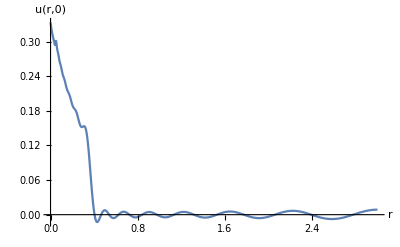

```mathematica
pR2 = Plot[fofrt[r, Pi], {r, 0, R}, PlotRange -> All, AxesLabel ->{r, "u(r,0)"}] (* Plot at θ = 0 *)
```

```mathematica
(* make a list of triples *)
rN = 100;
θN =7*24;
R = 1;
k = 5;
rL = Table[r, {r, R/rN,R, R/rN}]; (* Might want to do Sqrt[r] *)
θL = Table[θ, {θ, 2Pi/θN,2Pi, 2Pi/θN}]; (* Might not want 0 and 2Pi *)
fofrList = N@Table[f10[rL_[[i]], k, R], {i, 1, Length[rL]}];
fofθList = N@Table[Sin[k θL_[[i]]], {i, Length[θL]}];
dataVal = Outer[Times,fofrList, fofθList];
fofrList = N@Table[f01[rL_[[i]], k, R], {i, 1, Length[rL]}];
fofθList = N@Table[Cos[k θL_[[i]]], {i, 1Length[θL]}];
dataDer = Outer[Times,fofrList, fofθList];
uArray =dataVal - k dataDer;  (* PolarWaveVortex5 *)
uArray =-k dataDer ;  (* PolarWaveDer5 *)
uArray = dataVal ;  (* PolarWaveMode5 *)
uL = Flatten[uArray];
xL = Flatten@N@Table[rL_[[i]] Cos[θL_[[j]]], {i, 1, Length[rL]},{j, Length[θL]}];
yL = Flatten@N@Table[rL_[[i]] Sin[θL_[[j]]], {i, 1, Length[rL]},{j, Length[θL]}];
fig = ListPlot3D[Transpose[{xL, yL, uL}] , ViewPoint ->{3,2,4}]
```

-Graphics3D-

```mathematica
(*
Export["/Users/jimswift/Dropbox/student_seminar/PolarWaveMode5.pdf", fig]
*)
```